```mathematica
Series[1/(1-x^2),{x,0,10}]
```

1+x^2+x^4+x^6+x^8+x^10+O[x]^11

```mathematica
pex[z_,n_]:=Pochhammer[z,n]/n!
pez[z_,n_,d_]:=Product[(z+d (k-1))/k,{k,1,n}]
peza[z_,n_,d_]:=Product[(d z+d (k-1))/k,{k,1,n}]
pezb[z_,n_,d_]:=d^n Product[(z+(k-1))/k,{k,1,n}]
pez2[z_,n_,d_]:=d^n Pochhammer[z,n]/n!
pez3[z_,n_,d_]:=d^n Sum[Binomial[z-1,k] Binomial[n,k],{k,0,Infinity}]
```

```mathematica
Table[pex[2,Floor[n/2]]-pex[2,Floor[(n-1)/2]],{n,0,10}]
```

{1,0,1,0,1,0,1,0,1,0,1}

```mathematica
Series[(1-(3/2) x)^-(2),{x,0,10}]
```

1+3 x+(27 x^2)/4+(27 x^3)/2+(405 x^4)/16+(729 x^5)/16+(5103 x^6)/64+(2187 x^7)/16+(59049 x^8)/256+(98415 x^9)/256+(649539 x^10)/1024+O[x]^11

```mathematica
f1[z_,x_,m_]:=Sum[Binomial[z,k]m^k Binomial[x,k],{k,0,Infinity}]
```

```mathematica
Table[f1[z,x,m]-f1[z,x-1,m]/.m->3/.z->1,{x,1,10}]
```

{3,3,3,3,3,3,3,3,3,3}

```mathematica
f2[z_,x_,m_]:=Sum[Binomial[z,k]m^k  Binomial[x,k],{k,0,Infinity}]
```

```mathematica
Table[f2[z,x,m]-f2[z,x-1,m]/.m->3/.z->1,{x,1,10}]
```

{3,3,3,3,3,3,3,3,3,3}

```mathematica
Table[pez3[2,x,3/2],{x,0,10}]
```

{1,3,27/4,27/2,405/16,729/16,5103/64,2187/16,59049/256,98415/256,649539/1024}

```mathematica
FullSimplify@Sum[3 3 3,{r,1,x},{u,1,x-r},{v,1,x-r-u}]
```

9/2 (-2+x) (-1+x) x

```mathematica
FullSimplify@Sum[3 3 3 3,{r,1,x},{u,1,x-r},{v,1,x-r-u}, {w,1,x-r-u-v}]
```

27/8 (-3+x) (-2+x) (-1+x) x

```mathematica
FullSimplify@Sum[3 3,{r,1,x},{u,1,x-r}]
```

9/2 (-1+x) x

```mathematica
FullSimplify@Sum[3,{r,1,x}]
```

3 x

```mathematica
peza[12,3,3]
```

9828

```mathematica
pez2[12,3,3]
```

9828

```mathematica
FullSimplify[d^n Sum[Binomial[z-1,k] Binomial[n,k],{k,0,Infinity}]]
```

(d^n Gamma[n+z])/(Gamma[1+n] Gamma[z])

```mathematica
(d^n Gamma[n+z])/(Gamma[1+n] Gamma[z])/.n->k
```

(d^k Gamma[k+z])/(Gamma[1+k] Gamma[z])

```mathematica
FullSimplify[Sum[(d^k Gamma[k+z])/(Gamma[1+k] Gamma[z]),{k,0,n}]]
```

(1-d)^-z-(d^(1+n) Gamma[1+n+z] Hypergeometric2F1Regularized[1,1+n+z,2+n,d])/Gamma[z]

```mathematica
Sum[d^r Binomial[z-1,k] Binomial[r,k],{k,0,Infinity},{r,0,n}]
```

∑_(k=0)^∞ ∑_(r=0)^n d^r Binomial[r,k] Binomial[-1+z,k]

```mathematica
Sum[d^r Binomial[z-1,k] Binomial[r,k],{k,0,Infinity}]
```

(d^r Gamma[r+z])/(Gamma[1+r] Gamma[z])

```mathematica
FullSimplify[Sum[d^r Binomial[z-1,k] Binomial[r,k],{r,0,n}]]
```

Binomial[-1+z,k] (Binomial[0,k] Hypergeometric2F1[1,1,1-k,d]-d^(1+n) Binomial[1+n,k] Hypergeometric2F1[1,2+n,2-k+n,d])

```mathematica
Sum[d^t,{t,1,x}]
```

(d (-1+d^x))/(-1+d)

```mathematica
FullSimplify@Sum[d^(t+u),{t,1,x},{u,1,x-t}]
```

(d (d+d^x (d (-1+x)-x)))/(-1+d)^2

```mathematica
FullSimplify@Sum[d^(t+u+v),{t,1,x},{u,1,x-t},{v,1,x-t-u}]
```

(-2 d^3+d^(1+x) (d^2 (-2+x) (-1+x)-2 d (-2+x) x+(-1+x) x))/(2 (-1+d)^3)

```mathematica
FullSimplify@Sum[d^(t+u+v+w),{t,1,x},{u,1,x-t},{v,1,x-t-u},{w,1,x-t-u-v}]
```

(6 d^4+d^(1+x) (-6 d^3+(-1+d) (2+d (-7+11 d)) x-3 (-1+d)^2 (-1+2 d) x^2+(-1+d)^3 x^3))/(6 (-1+d)^4)

```mathematica
Clear[ez]
ez[n_,z_,d_]:=(1-d)^-z-(d^(1+n) Gamma[1+n+z] Hypergeometric2F1Regularized[1,1+n+z,2+n,d])/Gamma[z]
e2[n_,k_,d_]:=Sum[(-1)^(k-j)Binomial[k,j]ez[n,j,d],{j,0,k}]
```

```mathematica
ez[3,1,4]
```

85

```mathematica
e2[n,1,d]
```

-1+1/(1-d)-d^(1+n)/(1-d)

```mathematica
FullSimplify[e2[x,k,d],{Element[k,Integers],Element[x,Integers]}]
```

(-1)^k ((d/(-1+d))^k-d^(1+x) DifferenceRoot[Function[{y,n},{(-1-n+k) (-n+k) (1+n+x) y[n]-(-1-n+k) (-2-5 n-3 n^2+d+2 n d+n^2 d+k+n k-x-2 n x+d x+n d x+k x) y[1+n]+(1+n) (4+7 n+3 n^2-3 d-5 n d-2 n^2 d-2 k-2 n k+d k+n d k+x+n x-d x-n d x-k x+d k x) y[2+n]+(1+n)^2 (2+n) (-1+d) y[3+n]==0,y[0]==0,y[1]==0,y[2]==k/(-1+d)}]][1+k])

```mathematica
Integrate[d^t,{t,0,x}]
```

(-1+d^x)/Log[d]

```mathematica
FullSimplify[Integrate[d^(t+u),{t,0,x},{u,0,x-t}],{Element[x,Integers]}]
```

(1+d^x (-1+x Log[d]))/Log[d]^2

```mathematica
FullSimplify@Integrate[d^(t+u+v),{t,0,x},{u,0,x-t},{v,0,x-t-u}]
```

(-2+d^x (2+x Log[d] (-2+x Log[d])))/(2 Log[d]^3)

```mathematica
FullSimplify@Integrate[d^(t+u+v+w),{t,0,x},{u,0,x-t},{v,0,x-t-u},{w,0,x-t-u-v}]
```

(6+d^x (-6+x Log[d] (6+x Log[d] (-3+x Log[d]))))/(6 Log[d]^4)

```mathematica
(d (-1+d^x))/(-1+d)
```

```mathematica
(d (d+d^x (d (-1+x)-x)))/(-1+d)^2
```

```mathematica
(-2 d^3+d^(1+x) (d^2 (-2+x) (-1+x)-2 d (-2+x) x+(-1+x) x))/(2 (-1+d)^3)
```

```mathematica
(6 d^4+d^(1+x) (-6 d^3+(-1+d) (2+d (-7+11 d)) x-3 (-1+d)^2 (-1+2 d) x^2+(-1+d)^3 x^3))/(6 (-1+d)^4)
```

```mathematica
Expand[(6 d^4+d^(1+x) (-6 d^3+(-1+d) (2+d (-7+11 d)) x-3 (-1+d)^2 (-1+2 d) x^2+(-1+d)^3 x^3))/(6 (-1+d)^4)]
```

d^4/(-1+d)^4-d^(4+x)/(-1+d)^4-(d^(1+x) x)/(3 (-1+d)^4)+(3 d^(2+x) x)/(2 (-1+d)^4)-(3 d^(3+x) x)/(-1+d)^4+(11 d^(4+x) x)/(6 (-1+d)^4)+(d^(1+x) x^2)/(2 (-1+d)^4)-(2 d^(2+x) x^2)/(-1+d)^4+(5 d^(3+x) x^2)/(2 (-1+d)^4)-(d^(4+x) x^2)/(-1+d)^4-(d^(1+x) x^3)/(6 (-1+d)^4)+(d^(2+x) x^3)/(2 (-1+d)^4)-(d^(3+x) x^3)/(2 (-1+d)^4)+(d^(4+x) x^3)/(6 (-1+d)^4)

```mathematica
Expand@((-2 d^3+d^(1+x) (d^2 (-2+x) (-1+x)-2 d (-2+x) x+(-1+x) x))/(2 (-1+d)^3))
```

-d^3/(-1+d)^3+d^(3+x)/(-1+d)^3-(d^(1+x) x)/(2 (-1+d)^3)+(2 d^(2+x) x)/(-1+d)^3-(3 d^(3+x) x)/(2 (-1+d)^3)+(d^(1+x) x^2)/(2 (-1+d)^3)-(d^(2+x) x^2)/(-1+d)^3+(d^(3+x) x^2)/(2 (-1+d)^3)

```mathematica
Hypergeometric2F1Regularized[1,1+n+z,2+n,d]/.n->3.5/.z->2.3/.d->3
```

-0.00645408-2.75103×10^-6 ⅈ

```mathematica
Hypergeometric2F1[1,1+n+z,2+n,d]/Gamma[n+2]/.n->3.5/.z->2.3/.d->3
```

-0.00645408-2.75103×10^-6 ⅈ

```mathematica
Hypergeometric2F1[1,1+n+z,2+n,d]/Hypergeometric2F1Regularized[1,1+n+z,2+n,d]/.n->4/.z->2/.d->2
```

120

```mathematica
5!
```

120

```mathematica
Hypergeometric2F1[1,1+n+z,2+n,d]/.z->1
```

1/(1-d)

```mathematica
FullSimplify[ez[n,1,d]]
```

(-1+d^(1+n))/(-1+d)

```mathematica
FullSimplify[ez[n,-2,d]]
```

(-1+d)^2

```mathematica
Sum[(-1)^k Binomial[z,k](1-d)^k,{k,0,Infinity}]
```

d^z

```mathematica
Clear[a2]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
a2[n_,d_,0]:=UnitStep[n]
a2[n_,d_,k_]:=a2[n,d,k]=Sum[d^j a2[n-j,d,k-1],{j,1,n}]
az[n_,d_,z_]:=Sum[bin[z,k]a2[n,d,k],{k,0,n}]
a2o[n_,d_,k_]:=Sum[pex[j,k-1]d^(j+k-1),{j,0,n-k+1}]
a2alt[n_,d_,k_]:=(1-d)^-k d^k+1/Gamma[k](-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d]+d^(-1+k) Pochhammer[0,-1+k])
```

```mathematica
az[10,1,2]
```

66

```mathematica
(-1+d^(1+n))/(-1+d)/.n->10/.d->2
```

2047

```mathematica
FullSimplify[Sum[(d^k Gamma[k+z])/(Gamma[1+k] Gamma[z]),{k,0,n}]/.z->1]
```

(-1+d^(1+n))/(-1+d)

```mathematica
Table[az[n,3/2,2]-az[n-1,3/2,2],{n,0,10}]
```

{1,3,27/4,27/2,405/16,729/16,5103/64,2187/16,59049/256,98415/256,649539/1024}

```mathematica
Series[(1-(3/2) x)^-(2),{x,0,10}]
```

1+3 x+(27 x^2)/4+(27 x^3)/2+(405 x^4)/16+(729 x^5)/16+(5103 x^6)/64+(2187 x^7)/16+(59049 x^8)/256+(98415 x^9)/256+(649539 x^10)/1024+O[x]^11

```mathematica
Expand[az[10,3/2,z]-az[10-1,3/2,z]]
```

(59049 z)/10240+(46773369 z^2)/2867200+(8548983 z^3)/458752+(3297267 z^4)/286720+(1121931 z^5)/262144+(6589431 z^6)/6553600+(19683 z^7)/131072+(63423 z^8)/4587520+(6561 z^9)/9175040+(729 z^10)/45875200

```mathematica
Expand[a2[24,d,5]]
```

d^5+5 d^6+15 d^7+35 d^8+70 d^9+126 d^10+210 d^11+330 d^12+495 d^13+715 d^14+1001 d^15+1365 d^16+1820 d^17+2380 d^18+3060 d^19+3876 d^20+4845 d^21+5985 d^22+7315 d^23+8855 d^24

```mathematica
ar[n_,d_,k_]:=Sum[pex[j,k-1]d^(j+k-1),{j,0,n-k+1}]
```

```mathematica
ar[24,d,5]
```

d^5+5 d^6+15 d^7+35 d^8+70 d^9+126 d^10+210 d^11+330 d^12+495 d^13+715 d^14+1001 d^15+1365 d^16+1820 d^17+2380 d^18+3060 d^19+3876 d^20+4845 d^21+5985 d^22+7315 d^23+8855 d^24

```mathematica
Expand[a2[24,d,5]-ar[24,d,5]]
```

0

```mathematica
FullSimplify[ar[n,d,k],{Element[n,Integers],Element[k,Integers]}]
```

(1-d)^-k d^k+(-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d]+d^(-1+k) Pochhammer[0,-1+k])/Gamma[k]

```mathematica
Expand[a2[24,4,5]]
```

3139110873602135040

```mathematica
(1-d)^-k d^k+(-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d]+d^(-1+k) Pochhammer[0,-1+k])/Gamma[k]/.d->4/.k->5/.n->24
```

3139110873602135040

```mathematica
Limit[(1-d)^-k d^k+(-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d]+d^(-1+k) Pochhammer[0,-1+k])/Gamma[k]/.k->3,d->1]
```

1/6 n (2-3 n+n^2)

```mathematica
Sum[Binomial[z,k]((1-d)^-k d^k+(-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d]+d^(-1+k) Pochhammer[0,-1+k])/Gamma[k]),{k,0,Infinity}]
```

∑_(k=0)^∞ Binomial[z,k] ((1-d)^-k d^k+(-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d]+d^(-1+k) Pochhammer[0,-1+k])/Gamma[k])

```mathematica
Sum[Binomial[z,k]((1-d)^-k d^k),{k,0,Infinity}]
```

(-1/(-1+d))^z

```mathematica
Sum[Binomial[z,k]((d^(-1+k) Pochhammer[0,-1+k])/Gamma[k]),{k,0,Infinity}]
```

z

```mathematica
Sum[Binomial[z,k]((-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d])/Gamma[k]),{k,0,Infinity}]
```

∑_(k=0)^∞ -(d^(1+n) Binomial[z,k] Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d])/Gamma[k]

```mathematica
a2alta[10,3,4]
```

6344082

```mathematica
a2[10,3,4]
```

6344082

```mathematica
a2alta[n_,d_,k_]:=(1-d)^-k d^k+(-d^(1+n) Gamma[1+n] Hypergeometric2F1[1,1+n,2-k+n,d])/(Gamma[k](n+1-k)!)+d^(-1+k) Pochhammer[0,-1+k]/Gamma[k]
```

```mathematica
FullSimplify[Sum[Binomial[z,k]Sum[pex[j,k-1]d^(j+k-1),{j,0,n-k+1}],{k,0,n}],Element[n,Integers]]
```

-1/(n!)(1-d)^(-1-n) (n! ((1-d)^n (-1+d) ((1/(1-d))^z+z)+d^(1+n) Binomial[z,1+n] Hypergeometric2F1[1,1+n-z,2+n,d/(-1+d)])-(-1+d) (-(-1+d) d)^n (Binomial[z,1+n] HypergeometricPFQ[{1,n,1+n-z},{1+n,2+n},-d] Pochhammer[0,n]+d Gamma[1+n]^2 DifferenceRoot[Function[{y,n},{d (-n+n) (n-z) (1+n-z) y[n]-(1+n-z) (n+n^2-d-3 n d-3 n^2 d-n-n n+d n+2 n d n+n d z-d n z) y[1+n]+(1+n) (2+4 n+2 n^2-3 d-6 n d-3 n^2 d-n-n n+d n+n d n-n z+d z+2 n d z+n z-d n z) y[2+n]+(1+n)^2 (2+n) (-1+d) y[3+n]==0,y[0]==0,y[1]==0,y[2]==z/(Gamma[1+n]-d Gamma[1+n])}]][1+n]))

```mathematica
FullSimplify[Sum[Binomial[z,k]pex[j,k-1]d^(j+k-1),{k,0,n},{j,0,n-k+1}],Element[n,Integers]]
```

-1/Gamma[-n+z](1-d)^(-1-n) ((1-d)^n (-1+d) ((1/(1-d))^z+z) Gamma[-n+z]+d^(1+n) Gamma[1+z] Hypergeometric2F1Regularized[1,1+n-z,2+n,d/(-1+d)]-(-1+d) (-(-1+d) d)^n Gamma[-n+z] (Binomial[z,1+n] Gamma[2+n] HypergeometricPFQRegularized[{1,n,1+n-z},{1+n,2+n},-d] Pochhammer[0,n]+d Gamma[1+n] Gamma[1+z] DifferenceRoot[Function[{y,n},{d (-n+n) (n-z) (1+n-z) y[n]-(1+n-z) (n+n^2-d-3 n d-3 n^2 d-n-n n+d n+2 n d n+n d z-d n z) y[1+n]+(1+n) (2+4 n+2 n^2-3 d-6 n d-3 n^2 d-n-n n+d n+n d n-n z+d z+2 n d z+n z-d n z) y[2+n]+(1+n)^2 (2+n) (-1+d) y[3+n]==0,y[0]==0,y[1]==0,y[2]==1/(Gamma[1+n] Gamma[z]-d Gamma[1+n] Gamma[z])}]][1+n]))

```mathematica
bex[n_,z_,d_]:=∑_(k=0)^∞ Binomial[z,k] (-((1-d)^-k (-d^k Gamma[k] Gamma[2-k+n]+(1-d)^k d^(1+n) Gamma[1+n] Hypergeometric2F1[1,1+n,2-k+n,d]))/(Gamma[k] Gamma[2-k+n])+(d^(-1+k) Pochhammer[0,-1+k])/((-1+k)!))
```

```mathematica
Expand@az[10,1,3]
```

286

```mathematica
bex[10,1,3]
```

1/2

```mathematica
a2[10,2,2]
```

16388

```mathematica
a2o[10,2,2]
```

16388

```mathematica
a2o[n_,d_,k_]:=Sum[pex[j,k-1]d^(j+k-1),{j,0,n-k+1}]
a2oa[n_,d_,k_]:=Sum[Binomial[j-1,k-1]d^j,{j,1,n}]

a2oa[10,2,2]
```

16388

```mathematica
a2alt[10,2,2]
```

16388

```mathematica
a2oz[n_,d_,z_]:=Sum[Binomial[z,k]pex[j,k-1]d^(j+k-1),{k,0,Infinity},{j,0,n-k+1}]
```

```mathematica
a2or[n_,d_,k_]:=Table[pex[j,k-1]d^(j+k-1),{j,1,n-k+1}]
a2or2[n_,d_,k_]:=Table[pex[j,k-1]d^(j+k-1),{j,1,n}]
a2or3[n_,d_,k_]:=Table[pex[j-k+1,k-1]d^j,{j,1,n}]
a2or4[n_,d_,k_]:=Table[Binomial[j-1,k-1]d^j,{j,1,n}]
```

```mathematica
a2or[10,d,5]
```

{d^5,5 d^6,15 d^7,35 d^8,70 d^9,126 d^10}

```mathematica
a2or2[10,d,5]
```

{d^5,5 d^6,15 d^7,35 d^8,70 d^9,126 d^10,210 d^11,330 d^12,495 d^13,715 d^14}

```mathematica
a2or4[10,d,5]
```

{0,0,0,0,d^5,5 d^6,15 d^7,35 d^8,70 d^9,126 d^10}

```mathematica
Sum[d^t,{t,1,Infinity}]
```

-d/(-1+d)

```mathematica
Sum[d^(t+u),{t,1,Infinity},{u,1,Infinity}]
```

d^2/(-1+d)^2

```mathematica
(j-k+1)+k-1
```

j

```mathematica
FullSimplify[pex[j-k+1,k-1]]/.j->13/.k->5
```

495

```mathematica
Binomial[13-1,5-1]
```

495

```mathematica
Sum[Binomial[z,k]Sum[Binomial[j-1,k-1]d^j,{j,1,n}],{k,0,Infinity}]
```

```mathematica
Sum[Binomial[z,k]Sum[Binomial[j-1,k-1]d^j,{k,0,Infinity}],{j,1,n}]
```

```mathematica
Sum[Binomial[z,k]Binomial[j-1,k-1]d^j,{k,0,Infinity}]
```

(d^j z Gamma[j+z])/(Gamma[1+j] Gamma[1+z])

```mathematica
FullSimplify[Sum[(d^j z Gamma[j+z])/(Gamma[1+j] Gamma[1+z]),{j,0,n}]]
```

((1-d)^-z (Gamma[z]-(Beta[d,1+n,z] Gamma[1+n+z])/Gamma[1+n]))/Gamma[z]

```mathematica
az[13,-2,-2.5]
```

16.5293

```mathematica
((1-d)^-z (Gamma[z]-(Beta[d,1+n,z] Gamma[1+n+z])/Gamma[1+n]))/Gamma[z]/.n->13/.d->-2/.z->-2.5
```

16.5293

```mathematica
(1-d)^-z((Gamma[z])/Gamma[z]-((Beta[d,1+n,z] Gamma[1+n+z])/Gamma[1+n])/Gamma[z])/.n->13/.d->-2/.z->-2.5
```

16.5293

```mathematica
(1-d)^-z(1- ((Beta[d,1+n,z] Gamma[1+n+z])/(Gamma[1+n]Gamma[z])))/.n->13/.d->-2/.z->-2.5
```

16.5293

```mathematica
(1-d)^-z(1- ((Beta[d,1+n,z] Gamma[1+n+z])/(Gamma[1+n]Gamma[z])))/.n->13/.d->-2/.z->-2.5
```

```mathematica
Gamma[1+n+z]/(Gamma[1+n]Gamma[z])/.n->5/.z->3
```

168

```mathematica
(n+z)pex[z,n]/.n->5/.z->3
```

168

```mathematica
(1-d)^-z(1- ((z+n)pex[z,n]Beta[d,1+n,z] ))/.n->13/.d->-2/.z->-2.5
```

16.5293

```mathematica
Limit[(1-d)^-z(1- ((z+n)pex[z,n]Beta[d,1+n,z] )),d->1]
```

Limit[(1-d)^-z (1-((n+z) Beta[d,1+n,z] Pochhammer[z,n])/(n!)),d→1]

```mathematica
azalt[n_,d_,z_]:=(1-d)^-z(1- ((z+n)pex[z,n]Beta[d,1+n,z] ))
```

```mathematica
Expand@FullSimplify@Expand[azalt[10,3/2,z]-az[10-1,3/2,z]]
```

(59049 z)/10240+(46773369 z^2)/2867200+(8548983 z^3)/458752+(3297267 z^4)/286720+(1121931 z^5)/262144+(6589431 z^6)/6553600+(19683 z^7)/131072+(63423 z^8)/4587520+(6561 z^9)/9175040+(729 z^10)/45875200

```mathematica
Expand[az[10,3/2,z]-az[10-1,3/2,z]]
```

(59049 z)/10240+(46773369 z^2)/2867200+(8548983 z^3)/458752+(3297267 z^4)/286720+(1121931 z^5)/262144+(6589431 z^6)/6553600+(19683 z^7)/131072+(63423 z^8)/4587520+(6561 z^9)/9175040+(729 z^10)/45875200

```mathematica
Series[(1-(3/2) x)^-(2),{x,0,10}]
```

1+3 x+(27 x^2)/4+(27 x^3)/2+(405 x^4)/16+(729 x^5)/16+(5103 x^6)/64+(2187 x^7)/16+(59049 x^8)/256+(98415 x^9)/256+(649539 x^10)/1024+O[x]^11

```mathematica
Table[azalt[n,3/2,2]-azalt[n-1,3/2,2],{n,0,10}]
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{Indeterminate,3,27/4,27/2,405/16,729/16,5103/64,2187/16,59049/256,98415/256,649539/1024}

```mathematica
FullSimplify[azalt[n,d,z]-azalt[n-1,d,z]]
```

(d^n Gamma[n+z])/(Gamma[1+n] Gamma[z])

```mathematica
a2o[n_,d_,k_]:=Sum[pex[j,k-1]d^(j+k-1),{j,0,n-k+1}]
a2oa[n_,d_,k_]:=Sum[Binomial[j-1,k-1]d^j,{j,1,n}]
```

```mathematica
Sum[Binomial[j-1,k-1]d^j,{j,1,n}]
```

d (Binomial[0,-1+k] Hypergeometric2F1[1,1,2-k,d]-d^n Binomial[n,-1+k] Hypergeometric2F1[1,1+n,2-k+n,d])

```mathematica
Expand[d (Binomial[0,-1+k] Hypergeometric2F1[1,1,2-k,d]-d^n Binomial[n,-1+k] Hypergeometric2F1[1,1+n,2-k+n,d])]
```

d Binomial[0,-1+k] Hypergeometric2F1[1,1,2-k,d]-d^(1+n) Binomial[n,-1+k] Hypergeometric2F1[1,1+n,2-k+n,d]

```mathematica
d (Binomial[0,-1+k] Hypergeometric2F1[1,1,2-k,d]-d^n Binomial[n,-1+k] Hypergeometric2F1[1,1+n,2-k+n,d])/.k->3.0000001/.n->10/.d->2.0000001
```

59384.+2.91021×10^-10 ⅈ

```mathematica
a2o[10,2,3]
```

59384

```mathematica
(1-d)^-k d^k+(-d^(1+n) Gamma[1+n] Hypergeometric2F1Regularized[1,1+n,2-k+n,d]+d^(-1+k) Pochhammer[0,-1+k])/Gamma[k]/.n->10/.k->3/.d->2
```

59384

```mathematica
Table[Limit[D[d^x pex[z,x],z],z->0],{x,0,10}]
```

{0,d,d^2/2,d^3/3,d^4/4,d^5/5,d^6/6,d^7/7,d^8/8,d^9/9,d^10/10}

```mathematica
FullSimplify@Sum[d^k/k,{k,1,x}]
```

-d^(1+x) LerchPhi[d,1,1+x]-Log[1-d]

```mathematica
Clear[a2]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
a2[n_,d_,0]:=UnitStep[n]
a2[n_,d_,k_]:=a2[n,d,k]=Sum[d^j a2[n-j,d,k-1],{j,1,n}]
az[n_,d_,z_]:=Sum[bin[z,k]a2[n,d,k],{k,0,n}]
```

```mathematica
Table[Expand@D[az[11,d,z],{d,k}]/.d->0,{k,0,12}]//TableForm
```

1
z
z+z^2
2 z+3 z^2+z^3
6 z+11 z^2+6 z^3+z^4
24 z+50 z^2+35 z^3+10 z^4+z^5
120 z+274 z^2+225 z^3+85 z^4+15 z^5+z^6
720 z+1764 z^2+1624 z^3+735 z^4+175 z^5+21 z^6+z^7
5040 z+13068 z^2+13132 z^3+6769 z^4+1960 z^5+322 z^6+28 z^7+z^8
40320 z+109584 z^2+118124 z^3+67284 z^4+22449 z^5+4536 z^6+546 z^7+36 z^8+z^9
362880 z+1026576 z^2+1172700 z^3+723680 z^4+269325 z^5+63273 z^6+9450 z^7+870 z^8+45 z^9+z^10
3628800 z+10628640 z^2+12753576 z^3+8409500 z^4+3416930 z^5+902055 z^6+157773 z^7+18150 z^8+1320 z^9+55 z^10+z^11
0

```mathematica
Expand[D[az[10,d,z],z]/.z->0]
```

d+d^2/2+d^3/3+d^4/4+d^5/5+d^6/6+d^7/7+d^8/8+d^9/9+d^10/10

```mathematica
Expand@D[az[10,d,z],{z,2}]/.z->0
```

d^2+d^3+(11 d^4)/12+(5 d^5)/6+(137 d^6)/180+(7 d^7)/10+(363 d^8)/560+(761 d^9)/1260+(7129 d^10)/12600

```mathematica
Expand[D[az[10,d,z],{z,3}]/.z->0]
```

d^3+(3 d^4)/2+(7 d^5)/4+(15 d^6)/8+(29 d^7)/15+(469 d^8)/240+(29531 d^9)/15120+(1303 d^10)/672

```mathematica
Series[Log[1/(1-x)]^3,{x,0,10}]
```

x^3+(3 x^4)/2+(7 x^5)/4+(15 x^6)/8+(29 x^7)/15+(469 x^8)/240+(29531 x^9)/15120+(1303 x^10)/672+O[x]^11

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,d_,z_]:= Product[d^p[[2]](-1)^p[[2]]Binomial[-z,p[[2]]],{p,FI[n]}]
dza[n_,d_,z_]:= Product[d^p[[2]]pex[z,p[[2]]],{p,FI[n]}]
Dza[n_,d_,z_]:= Sum[dza[j,d,z],{j,1,n}]
dzax[n_,d_]:= Product[d^p[[2]],{p,FI[n]}]
```

```mathematica
Table[D[dza[n,d,1],d]/.d->0,{n,1,20}]//TableForm
```

0
1
1
0
1
0
1
0
0
0
1
0
1
0
0
0
1
0
1
0

```mathematica
Sum[D[dzax[n,d],d]/.d->0,{n,1,100}]
```

25

```mathematica
az[10,d,1]
```

1+d+d^2+d^3+d^4+d^5+d^6+d^7+d^8+d^9+d^10

```mathematica
Product[1/(1-Prime[p]^-s),{p,1,Infinity}]
```

Zeta[s]

```mathematica
Product[1/(1-d Prime[p]^-s),{p,1,Infinity}]
```

∏_(p=1)^∞ 1/(1-d Prime[p]^-s)

```mathematica
Table[Sum[dza[n,d,1],{n,1,m}]/.d->-1,{m,1,30}]
```

{1,0,-1,0,-1,0,-1,-2,-1,0,-1,-2,-3,-2,-1,0,-1,-2,-3,-4,-3,-2,-3,-2,-1,0,-1,-2,-3,-4}

```mathematica
1+25+34+22+12+4+2
```

100

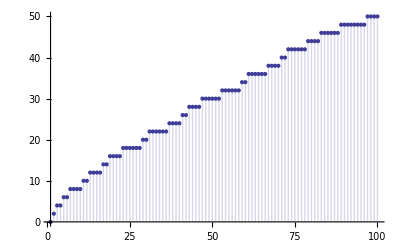

```mathematica
DiscretePlot[D[Dza[n,d,2],d]/.d->0,{n,1,100}]
```

```mathematica
Dza[100,d,2]
```

1+50 d+132 d^2+138 d^3+104 d^4+38 d^5+19 d^6

```mathematica
1+50+132+138+104+38+19
```

482

```mathematica
(* OH HO!!!! D_2(100) = 482*)
```

```mathematica
Expand@D[Dza[100,d,z],z]/.z->0
```

25 d+2 d^2+(2 d^3)/3+d^4/2+d^5/5+d^6/6

```mathematica
1+75+294+425+414+171+91
```

1471

```mathematica
(* OH HO!!!! D_3(100) = 1471*)
```

```mathematica
Dza[100,d,1]
```

1+25 d+34 d^2+22 d^3+12 d^4+4 d^5+2 d^6

```mathematica
Sum[z^PrimeOmega[j],{j,1,1000000}]
```

1+78498 z+210035 z^2+250853 z^3+198062 z^4+124465 z^5+68963 z^6+35585 z^7+17572 z^8+8491 z^9+4016 z^10+1878 z^11+865 z^12+400 z^13+179 z^14+79 z^15+35 z^16+14 z^17+7 z^18+2 z^19

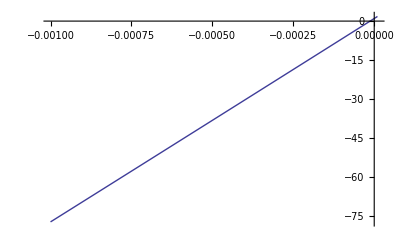

```mathematica
Plot[1+78498 z+210035 z^2+250853 z^3+198062 z^4+124465 z^5+68963 z^6+35585 z^7+17572 z^8+8491 z^9+4016 z^10+1878 z^11+865 z^12+400 z^13+179 z^14+79 z^15+35 z^16+14 z^17+7 z^18+2 z^19,{z,-.001,.00001}]
```

```mathematica
N@-1/78498
```

-0.0000127392

```mathematica
po[n_,z_]:=po[n,z]=Sum[z^PrimeOmega[j],{j,1,n}]
roots[n_]:=If[(c=Exponent[f=po[n,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
rootsa[n_]:=If[(c=Exponent[f=po[n,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
roots[1000000]
```

{-1.97948,-1.6502-0.279432 ⅈ,-1.6502+0.279432 ⅈ,-1.35322-0.91163 ⅈ,-1.35322+0.91163 ⅈ,-1.03853,-1.00251-1.37925 ⅈ,-1.00251+1.37925 ⅈ,-0.509696-1.73536 ⅈ,-0.509696+1.73536 ⅈ,-0.0000127396,0.109282-1.87708 ⅈ,0.109282+1.87708 ⅈ,0.792341-1.80882 ⅈ,0.792341+1.80882 ⅈ,1.4363-1.48823 ⅈ,1.4363+1.48823 ⅈ,1.93672-0.901739 ⅈ,1.93672+0.901739 ⅈ}

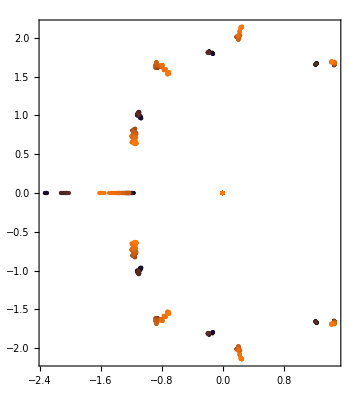

```mathematica
Graphics[Table[{ColorData["RustTones"][((n-1000)/100)],Point[{Re[#],Im[#]}]}&/@roots[n],{n,1000+0,1000+100}],Frame->True]
```

```mathematica
Sum[-1/r,{r,roots[10000]}]
```

1229.+0. ⅈ

```mathematica
Product[1-1/r,{r,roots[10000]}]
```

10000.-4.54747×10^-13 ⅈ

```mathematica
roots[1000000]//TableForm
```

-1.97948
-1.6502-0.279432 ⅈ
-1.6502+0.279432 ⅈ
-1.35322-0.91163 ⅈ
-1.35322+0.91163 ⅈ
-1.03853
-1.00251-1.37925 ⅈ
-1.00251+1.37925 ⅈ
-0.509696-1.73536 ⅈ
-0.509696+1.73536 ⅈ
-0.0000127396
0.109282-1.87708 ⅈ
0.109282+1.87708 ⅈ
0.792341-1.80882 ⅈ
0.792341+1.80882 ⅈ
1.4363-1.48823 ⅈ
1.4363+1.48823 ⅈ
1.93672-0.901739 ⅈ
1.93672+0.901739 ⅈ

```mathematica
po[120,z]
```

1+30 z+39 z^2+28 z^3+13 z^4+7 z^5+2 z^6

```mathematica
Dd[96,x]
```

1+(413 x)/15+(15839 x^2)/360+(307 x^3)/16+(575 x^4)/144+(67 x^5)/240+(7 x^6)/720

```mathematica
rootPlot[poly_,x_,opts___]/;PolynomialQ[poly,x]:=ListPlot[Map[Composition[Through,{Re,Im}],x/.NSolve[poly,x]],opts,AspectRatio->Automatic]
Animate[rootPlot[po[n,x],x,Axes->None,PlotRange->{{-3,2},{-3,3}},PlotRangeClipping->True, Frame->True,PlotStyle->AbsolutePointSize[6]],{n,10000,10020}]
```

```mathematica
Animate[DiscretePlot[Re@po[n,z]/.z->k+1.I,{n,1,2000}],{k,-2,1}]
```

```mathematica
Limit[po[n,I],n->Infinity]
```

Limit[∑_(j=1)^n ⅈ^PrimeOmega[j],n→∞]

```mathematica
ba[n_,z_]:=Product[1/(1-z),{j,1,n}]
ba2[n_,z_]:=(1/(1-z))^n
```

```mathematica
Plot[{ba2[500,z]},{z,-2,2}]
```

-Graphics-

```mathematica
Limit[(1/(1-(1+1/2-(√3)/2 I)))^n,n->Infinity]
```

ⅇ^(2 ⅈ Interval[{0,π}])

```mathematica
N@Abs[1/2-8/10 I]
```

0.943398

```mathematica
(1-(1/2)^2)^(1/2)
```

(√3)/2

```mathematica
(1-(1/2)^2)^(1/2)
```

(√3)/2

```mathematica
Limit[(1/(1-(1+2/3-(√5)/3 I )))^n,n->Infinity]
```

ⅇ^(2 ⅈ Interval[{0,π}])

```mathematica
Animate[DiscretePlot[Im@po[n,(1+Cos[x]+I Sin[x] )],{n,1,100}],{x,3,3.2}]
```

```mathematica
po[100,z]/.z->1+Cos[Pi]+I Sin[Pi]
```

1

```mathematica
1+Cos[Pi]+I Sin[Pi]
```

0

```mathematica
Product[1/(1-d Prime[p]^-s),{p,1,Infinity}]/.d->-1
```

Zeta[2 s]/Zeta[s]

```mathematica
Product[1/(1-d Prime[p]^-s),{p,1,Infinity}]/.d->1
```

Zeta[s]

```mathematica
Product[1/(1-d Prime[p]^-s),{p,1,Infinity}]/.d->-2
```

∏_(p=1)^∞ 1/(1+2 Prime[p]^-s)

```mathematica
Product[1/(1-d Prime[p]^-s),{p,1,Infinity}]/.d->0
```

1

```mathematica
2 HarmonicNumber[4]+HarmonicNumber[3]+3/2 HarmonicNumber[2] + 29/12 HarmonicNumber[1]
```

32/3

```mathematica
a[n_]:=1/n Sum[MoebiusMu[n/d](-2)^d,{d,Divisors[n]}]
at[n_,t_]:=1/n Sum[ MoebiusMu[n/d]t^d,{d,Divisors[n]}]
```

```mathematica
Table[at[n,-2],{n,1,8}]
```

{-2,3,-2,3,-6,11,-18,30}

```mathematica
{Sum[at[j,-4]HarmonicNumber[Floor[20/j]],{j,1,20}],Sum[(-4)^j/j,{j,1,20}]}
```

{126660844867346380/2909907,126660844867346380/2909907}

```mathematica
a3[n_]:=1/n Sum[ MoebiusMu[n/d](-3)^d,{d,Divisors[n]}]
```

```mathematica
Table[a3[n],{n,1,8}]
```

{-3,6,-8,18,-48,124,-312,810}

```mathematica
a3p[n_]:=1/n Sum[ MoebiusMu[n/d]3^d,{d,Divisors[n]}]
```

```mathematica
Table[a3p[n],{n,1,8}]
```

{3,3,8,18,48,116,312,810}

```mathematica
a2p[n_]:=1/n Sum[ MoebiusMu[n/d]2^d,{d,Divisors[n]}]
```

```mathematica
Table[a2p[n],{n,1,8}]
```

{2,1,2,3,6,9,18,30}

```mathematica
am[n_]:=1/n Sum[ MoebiusMu[n/d](-1)^d,{d,Divisors[n]}]
```

```mathematica
Table[am[n],{n,1,8}]
```

{-1,1,0,0,0,0,0,0}

```mathematica
Sum[MoebiusMu[n]Log[1+2 x^n]/n,{n,1,Infinity}]
```

∑_(n=1)^∞ (Log[1+2 x^n] MoebiusMu[n])/n

```mathematica
at[n_,t_]:=1/n Sum[ MoebiusMu[n/d]t^d,{d,Divisors[n]}]
```

```mathematica
Product[(1+x/k)^at[k,-2],{k,1,16}]
```

((1+x/16)^4080 (1+x/14)^1179 (1+x/12)^335 (1+x/10)^105 (1+x/8)^30 (1+x/6)^11 (1+x/4)^3 (1+x/2)^3)/((1+x/15)^2182 (1+x/13)^630 (1+x/11)^186 (1+x/9)^56 (1+x/7)^18 (1+x/5)^6 (1+x/3)^2 (1+x)^2)

```mathematica
Product[(1+x/k)^(MoebiusMu[k]/k),{k,1,16}]
```

((1+x/15)^(1/15) (1+x/14)^(1/14) (1+x/10)^(1/10) (1+x/6)^(1/6) (1+x))/((1+x/13)^(1/13) (1+x/11)^(1/11) (1+x/7)^(1/7) (1+x/5)^(1/5) (1+x/3)^(1/3) √(1+x/2))

```mathematica
N[Product[Zeta[k s]^at[k,-3],{k,1,24}]/.s->2.5]
```

0.497552

```mathematica
N@Product[1/(1-(-3)Prime[p]^-2.5),{p,1,100000}]
```

0.497552

```mathematica
N[Product[1/(1-x^k)^at[k,-2],{k,1,Infinity}]/.x->.5]
```

$Aborted

```mathematica
Sum[t^j,{j,0,x}]
```

(-1+t^(1+x))/(-1+t)

```mathematica
1+Integrate[t^Log[y],{y,2,x}]
```

ConditionalExpression[1-(2^(1+Log[t])-t^Log[x] x)/(1+Log[t]),Re[x]≥0||x∉Reals]

```mathematica
D[1-(2^(1+Log[t])-t^Log[x] x)/(1+Log[t]),t]/.x->100./.t->0.0000001
```

14.1225

```mathematica
at[n_,t_]:=1/n Sum[ MoebiusMu[n/d]t^d,{d,Divisors[n]}]
```

```mathematica
Expand@Table[{D[at[n,t],t]/.t->0, MoebiusMu[n]/n},{n,1,10}]//TableForm
```

1 | 1
-1/2 | -1/2
-1/3 | -1/3
0 | 0
-1/5 | -1/5
1/6 | 1/6
-1/7 | -1/7
0 | 0
0 | 0
1/10 | 1/10

```mathematica
N@Sum[2^PrimeNu[j]/j^2,{j,1,10000}]
```

2.49924

```mathematica
Zeta[2]^2/Zeta[2 2]
```

5/2

```mathematica
N@Sum[4^PrimeNu[j]/j^2,{j,1,100000}]
```

4.99828

```mathematica
N@Zeta[2 2]^2/Zeta[2 4]
```

1.16667

```mathematica
1+Sum[t^PrimeOmega[j],{j,2,10}]
```

1+4 t+4 t^2+t^3

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:= Product[(-1)^p[[2]]Binomial[-z,p[[2]]],{p,FI[n]}]
om1[n_,t_]:= Product[t^p[[2]],{p,FI[n]}]
om2[n_,t_]:=t^PrimeOmega[n]
pr[n_,t_,i_]:=If[Prime[i]>n,1,Sum[t^k pr[n/Prime[i]^k,t,i+1],{k,0,Log[Prime[i],n]}]]
pr2[n_,t_]:=Sum[om1[j,t],{j,1,n}]
pr3[n_,t_]:=Sum[om2[j,t],{j,1,n}]
```

```mathematica
Table[{om1[n,t],om2[n,t]},{n,1,10}]//TableForm
```

1 | 1
t | t
t | t
t^2 | t^2
t | t
t^2 | t^2
t | t
t^3 | t^3
t^2 | t^2
t^2 | t^2

```mathematica
Expand@pr[100,t,1]
```

1+25 t+34 t^2+22 t^3+12 t^4+4 t^5+2 t^6

```mathematica
pr2[100,t]
```

1+25 t+34 t^2+22 t^3+12 t^4+4 t^5+2 t^6

```mathematica
D[N[Product[Zeta[k s]^at[k,t],{k,1,30}]/.s->3.],t]/.t->0
```

0.174763

```mathematica
D[N@Product[1/(1-(t)Prime[p]^-3.),{p,1,100}],t]/.t->0
```

0.174762

```mathematica
N@Sum[If[PrimeQ[j]==True,1,0]/j^3,{j,1,1000}]
```

0.174763

```mathematica
N@Sum[If[PrimeQ[j]==True,1,0],{j,1,1000}]
```

168.

```mathematica
D[N[Product[Zeta[k s]^at[k,t],{k,1,40}]/.s->0.],t]/.t->0
```

-0.0349921+0.158597 ⅈ

```mathematica
D[N@Product[1/(1-t ),{p,1,200}],t]/.t->0
```

200.

```mathematica
Expand@Table[Sum[at[j,t],{j,1,n}],{n,1,6}]//TableForm
```

t
t/2+t^2/2
t/6+t^2/2+t^3/3
t/6+t^2/4+t^3/3+t^4/4
-t/30+t^2/4+t^3/3+t^4/4+t^5/5
(2 t)/15+t^2/12+t^3/6+t^4/4+t^5/5+t^6/6

```mathematica
ex[n_]:=Sum[t^k/k,{k,1,n}]
ex2[n_]:=Sum[MoebiusMu[j]/j ex[n/j],{j,1,n}]
ex3[n_]:=Sum[MoebiusMu[j]/j t^k/k,{j,1,n},{k,1,n/j}]
```

```mathematica
Product[1/(1-t Prime[p]^-s),{p,1,10}]
```

1/((1-2^-s t) (1-3^-s t) (1-5^-s t) (1-7^-s t) (1-11^-s t) (1-13^-s t) (1-17^-s t) (1-19^-s t) (1-23^-s t) (1-29^-s t))

```mathematica
Expand[D[Product[1/(1-t Prime[p]^-s),{p,1,4}],t]]
```

7^-s/((1-2^-s t) (1-3^-s t) (1-5^-s t) (1-7^-s t)^2)+5^-s/((1-2^-s t) (1-3^-s t) (1-5^-s t)^2 (1-7^-s t))+3^-s/((1-2^-s t) (1-3^-s t)^2 (1-5^-s t) (1-7^-s t))+2^-s/((1-2^-s t)^2 (1-3^-s t) (1-5^-s t) (1-7^-s t))

```mathematica
FullSimplify[29^-s / (1-29^-s t)]
```

1/(29^s-t)

```mathematica
Expand[D[Product[Zeta[k s]^at[k,t],{k,1,4}],t]]
```

Log[Zeta[s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))-1/2 Log[Zeta[2 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+t Log[Zeta[2 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))-1/3 Log[Zeta[3 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+t^2 Log[Zeta[3 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))-1/2 t Log[Zeta[4 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+t^3 Log[Zeta[4 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))

```mathematica
Log[Zeta[s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+
-1/2 Log[Zeta[2 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+
t Log[Zeta[2 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+
-1/3 Log[Zeta[3 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+
t^2 Log[Zeta[3 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+
-1/2 t Log[Zeta[4 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))+
t^3 Log[Zeta[4 s]] Zeta[s]^t Zeta[2 s]^(1/2 (-t+t^2)) Zeta[3 s]^(1/3 (-t+t^3)) Zeta[4 s]^(1/4 (-t^2+t^4))
```

```mathematica
Table[at[k,0],{k,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
D[1/(1-x),{x,1}]
```

1/(1-x)^2

```mathematica
D[1/(1-t p^-s),{t,1}]
```

p^-s/((1-p^-s t)^2)

```mathematica
D[Sum[t^k,{k,0,x}],t]/.t->0/.x->1
```

1

```mathematica
D[1+Integrate[t^k,{k,0,x}],t]
```

-(-1+t^x)/(t Log[t]^2)+(t^(-1+x) x)/Log[t]

```mathematica
lg[x_]:=-ExpIntegralEi[-x]+Log[x]+EulerGamma
lgs[x_,t_]:=Sum[ at[k,t]lg[x/k],{k,1,x}]
llg[x2_]:=Limit[LogIntegral[x]-Log[Log[x]]-EulerGamma,x->x2]
llgs[x_,t_]:=Sum[ at[k,t]llg[x/k],{k,1,x}]
```

```mathematica
N@lgs[100,t]/.t->-.5
```

-0.418736

```mathematica
Log[1/2.]
```

-0.693147

```mathematica
Log[1/(1-t)]/.t->-.5
```

-0.405465

```mathematica
E^-0.40546510810816444
```

0.666667

```mathematica
HarmonicNumber[1000.]
```

7.48547

```mathematica
N[HarmonicNumber[100]-HarmonicNumber[50]]
```

0.688172

```mathematica
Expand@llgs[100.,t]/.t->1
```

28.0217

```mathematica
h[n_,t_]:=Sum[t^( k)/( k),{k,1,n}]
hx[n_,t_,m_]:=Sum[t^(m k)/(m k),{k,1,n/m}]
hi[n_,t_]:=(Expand[hx[n,t,1]]-Expand[hx[10,t,2]]-Expand[hx[10,t,3]]-Expand[hx[10,t,5]]+Expand[hx[10,t,6]]-Expand[hx[10,t,7]]+Expand[hx[10,t,10]])/t
hi2[n_,t_]:=(hx[n,t,1]-hx[10,t,2]-hx[10,t,3]-hx[10,t,5]+hx[10,t,6]-hx[10,t,7]+hx[10,t,10])/t
hi3[n_,t_]:=Sum[MoebiusMu[k]/t hx[n,t,k],{k,1,n}]
hi4[n_,t_]:=(1/t)Sum[MoebiusMu[k]/k h[n/k,t^k],{k,1,n}]
```

```mathematica
Expand@hi4[20,t]
```

1

```mathematica
hx[10,t,2]
```

t^2/2+t^4/4+t^6/6+t^8/8+t^10/10

```mathematica
Expand[h[10/2,t^2]/2]
```

t^2/2+t^4/4+t^6/6+t^8/8+t^10/10

```mathematica
Table[Limit[at[n,t]/t,t->0],{n,1,10}]
```

{1,-1/2,-1/3,0,-1/5,1/6,-1/7,0,0,1/10}

```mathematica
h[100,.8]
```

1.60944

```mathematica
Log[1/(1-(.8))]
```

1.60944

```mathematica
h[n_,t_]:=Sum[t^( k)/( k),{k,1,n}]
ax[x_,t_,r_]:=1/t Sum[MoebiusMu[k]/k h[x/k,t^k],{k,1,r}]
axa[x_,t_]:=1/t Sum[MoebiusMu[k]/k h[x/k,t^k],{k,1,x}]
axb[t_,r_]:=1/t Sum[MoebiusMu[k]/k (-Log[1-t^k]),{k,1,r}]
axc[t_,r_]:=Product[(1/(1-t^k))^(MoebiusMu[k]/k/t),{k,1,r}]
axd[t_,z_,r_]:=Product[(1/(1-t^k))^(z MoebiusMu[k]/k/t),{k,1,r}]
```

```mathematica
Expand@axa[100,t]
```

1

```mathematica
Table[Limit[h[x/k,t^k],x->Infinity],{k,1,6}]
```

{Limit[-t^(1+x) LerchPhi[t,1,1+x]-Log[1-t],x→∞],Limit[-(t^2)^(1+x/2) LerchPhi[t^2,1,1+x/2]-Log[1-t^2],x→∞],Limit[-(t^3)^(1+x/3) LerchPhi[t^3,1,1+x/3]-Log[1-t^3],x→∞],Limit[-(t^4)^(1+x/4) LerchPhi[t^4,1,1+x/4]-Log[1-t^4],x→∞],Limit[-(t^5)^(1+x/5) LerchPhi[t^5,1,1+x/5]-Log[1-t^5],x→∞],Limit[-(t^6)^(1+x/6) LerchPhi[t^6,1,1+x/6]-Log[1-t^6],x→∞]}

```mathematica
axb[t,50]/.t->-.00000000001I
```

1.-5.×10^-12 ⅈ

```mathematica
axc[-.9,1000]
```

2.71828

```mathematica
Product[(1/(1-t^k))^(MoebiusMu[k]/k/t),{k,1,Infinity}]
```

$Aborted

```mathematica
axd[-.9,-1,1000]
```

0.367879

```mathematica
E^2.
```

7.38906

```mathematica
aa^(1/t)/.aa->2/.t->3
```

2^(1/3)

```mathematica
(.2^(1/3))^-3/2
```

2.5

```mathematica
Product[(1-z^k)^(MoebiusMu[k]/k),{k,1,Infinity}]
```

∏_(k=1)^∞ (1-z^k)^(MoebiusMu[k]/k)

```mathematica
FullSimplify[(1/(1-t^k))^(1/t)]
```

(1/(1-t^k))^(1/t)

```mathematica
bt[k_,t_]:=1/k Sum[ t^d,{d,Divisors[k]}]
h[n_,t_]:=Sum[t^k/ k,{k,1,n}]
sm[n_,t_]:=Sum[bt[k,t]h[n/k,t^k],{k,1,n}]
```

```mathematica
sm[10,2]
```

3299612/21

```mathematica
HarmonicNumber[6]
```

49/20

```mathematica
Expand[(h[4,t])]
```

t+t^2/2+t^3/3+t^4/4

```mathematica
Expand[h[4/2,(t-1)^2]]
```

3/2-4 t+4 t^2-2 t^3+t^4/2

```mathematica
Expand[h[4,t]]-Expand[h[4/2,t^2-t/2]-Expand[h[4/3,t^3-t/3]]]
```

(7 t)/6-(5 t^2)/8+(11 t^3)/6-t^4/4

```mathematica
HarmonicNumber[3]
```

11/6

```mathematica
er[x_,t_,u_]:=(1/t)Sum[u^k MoebiusMu[j]/j/k t^(j m)/m,{j,1,x},{k,1,x/j},{m,1,x/j/k}]
```

```mathematica
er[10,2,1]
```

7381/2520

```mathematica
Sum[2^k/k,{k,1,10}]
```

74752/315

```mathematica
axo[x_,t_]:=1/t Sum[MoebiusMu[k]/k Sum[t^(m k)/m,{m,1,x/k}],{k,1,x}]
```

```mathematica
Expand[axo[30,t]]
```

1

```mathematica
t^a Pochhammer[z/t,a]/a!/.a->1
```

z

```mathematica
t^(a+b) Pochhammer[z/t,a]/a!Pochhammer[z/t,b]/b!/.a->1/.b->1
```

z^2

```mathematica
Limit[FullSimplify@Expand[t^(a+b+c) Pochhammer[z/t,a]/a!Pochhammer[-z/t/2,b]/b!Pochhammer[-z/t/3,c]/c!/.a->2/.b->2/.c->2],t->0]
```

z^6/288

```mathematica
Limit[Pochhammer[MoebiusMu[4]/t,aa]/aa,t->0]/.aa->2
```

0

```mathematica
pex[z_,n_]:=Pochhammer[z,n]/n!
px[z_,n_,t_]:=t^n Pochhammer[z,n]/n!
```

```mathematica
ff[n_,t_,k_]:=If[k>n,1,Sum[ t^( j k) pex[MoebiusMu[k]/k/t,j]ff[n-k j,t,k+1],{j,0,n/k}]]
ez[n_,t_,k_]:=If[k>n,1,Sum[  t^( j k)Pochhammer[MoebiusMu[k]/k,j]/j! ez[n-k j,t,k+1],{j,0,n/k}]]
ackr2[n_,z_,k_]:=If[k>n,1,Sum[pex[z MoebiusMu[k]/k,j]ackr2[n-k j,z,k+1],{j,0,n/k}]]
ackr3[n_,z_,k_]:=If[k>n,1,Sum[pex[z MoebiusMu[k]/k,j] ackr3[n-k j,z,k+1],{j,0,n/k}]]
r2[n_,z_,k_]:=If[k>n,1,Sum[Pochhammer[z MoebiusMu[k]/k,j]/j! r2[n-k j,z,k+1],{j,0,n/k}]]
```

```mathematica
Expand@ez[10,t,1]
```

1+t+t^2/2+t^3/6+t^4/24+t^5/120+t^6/720+t^7/5040+t^8/40320+t^9/362880+t^10/3628800

```mathematica
N@E^I
```

0.540302+0.841471 ⅈ

```mathematica
Expand[(ez[10,t I,1]+ez[10,-t I,1])/2]
```

1-t^2/2+t^4/24-t^6/720+t^8/40320-t^10/3628800

```mathematica
(1-(t)^k)^a
```

(1-t^k)^a

```mathematica
Sum[t^(a k)/k,{k,1,Infinity}]
```

-Log[1-t^a]

```mathematica
Sum[t^k,{k,0,Infinity}]
```

1/(1-t)

```mathematica
Sum[t^(a k),{k,0,Infinity}]
```

-1/(-1+t^a)

```mathematica
re[t_,x_]:=Sum[t^k,{k,0,x}]
```

```mathematica
Table[D[re[t,5],{t,k}]/.t->0,{k,0,6}]
```

{1,1,2,6,24,120,0}

```mathematica
re[t,5]
```

1+t+t^2+t^3+t^4+t^5

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
ezz[n_,z_]:= Product[z^p[[2]]/(p[[2]]!),{p,FI[n]}]
Ezz[n_,z_]:=Sum[ezz[j,z],{j,1,n}]
Om[n_,t_]:=Sum[t^PrimeOmega[j],{j,1,n}]
```

```mathematica
D[Ezz[100,z],{z,6}]/.z->0
```

7

```mathematica
D[Om[100,z],{z,6}]/.z->0
```

1440

```mathematica
Log[E^2]
```

2

```mathematica
Log[Sin[Pi/6]]
```

-Log[2]

```mathematica
cs[n_,z_]:=Sum[(-1)^k z^(2k)/(2k)!,{k,0,n/2}]
es[n_,z_]:=Sum[z^k/(k!),{k,0,n}]
```

```mathematica
cs[10,z]
```

1-z^2/2+z^4/24-z^6/720+z^8/40320-z^10/3628800

```mathematica
Expand[(es[10,z I ]+es[10,-z I ])/2]
```

1-z^2/2+z^4/24-z^6/720+z^8/40320-z^10/3628800

```mathematica
Product[1/(1+(t I)^k)/.t->(1/2),{k,1,11}]
```

314194035692687583485586571264/298212483890845108013413359375-(32318102517423676521728442368 ⅈ)/80470035335624870416317890625

```mathematica
Product[1/(1+(-t I)^k)/.t->(-1/2),{k,1,11}]
```

314194035692687583485586571264/298212483890845108013413359375-(32318102517423676521728442368 ⅈ)/80470035335624870416317890625

```mathematica
pl[t_,r_]:=Product[(1/(1-t^k))^(MoebiusMu[k]/k),{k,1,r}]
pf[t_,r_]:=Table[(1/(1-(t I)^k))^(MoebiusMu[k]/k),{k,1,r}]
pf2[t_,r_]:=Table[(1/(1-(t I)^k))^(MoebiusMu[k]/k),{k,2,r,2}]
```

```mathematica
pl[-3I,5]
```

((1-3 ⅈ) 2^(1/30) 5^(7/30) 73^(1/3) 1181^(1/5))/((1+27 ⅈ)^(1/3) (1-243 ⅈ)^(1/5))

```mathematica
FullSimplify[Abs@pf[.9,20]//TableForm]
```

0.743294
1.34536
1.07362
1.
1.03036
0.931429
1.01482
1.
1.
0.97053
1.00428
1.
1.00241
0.985393
0.998617
1.
1.00081
1.
1.00048
1.

```mathematica
pls2[t_,r_]:=(1/2)(pl[t I,r]+pl[-t I,r])
pls3[t_,r_]:=Re[pl[t I,r]]
ez[n_,t_,k_]:=If[k>n,1,Sum[  t^( j k)Pochhammer[MoebiusMu[k]/k,j]/j! ez[n-k j,t,k+1],{j,0,n/k}]]
pls4[t_,r_]:=(1/2)(ez[r,t I,1]+ez[r,-t I,1])
```

```mathematica
N@pls3[.9,100]
```

0.62161

```mathematica
Cos[.9]
```

0.62161

```mathematica
Expand@pls4[t,20]
```

1-t^2/2+t^4/24-t^6/720+t^8/40320-t^10/3628800+t^12/479001600-t^14/87178291200+t^16/20922789888000-t^18/6402373705728000+t^20/2432902008176640000

```mathematica
Re[pls2[t,6]]
```

1/2 Re[((1/(1+t^6))^(1/6))/((1-ⅈ t) √(1/(1+t^2)) (1/(1+ⅈ t^3))^(1/3) (1/(1-ⅈ t^5))^(1/5))+((1/(1+t^6))^(1/6))/((1+ⅈ t) √(1/(1+t^2)) (1/(1-ⅈ t^3))^(1/3) (1/(1+ⅈ t^5))^(1/5))]

```mathematica
bex[n_,z_]:=Sum[Pochhammer[z,a]/a! Pochhammer[-z,b]/b!,{a,0,n},{b,0,(n-a)/2}]
bext[n_,z_,t_]:=Sum[t^a Pochhammer[z,a]/a! t^(2b) Pochhammer[-z,b]/b!,{a,0,n},{b,0,(n-a)/2}]
bext2[n_,z_,q_,k_]:=Sum[q^a Pochhammer[z,a]/a! q^(k b)  Pochhammer[-z,b]/b!,{a,0,n},{b,0,(n-a)/k}]
```

```mathematica
Expand@bex[20,7]
```

128

```mathematica
Expand@bext[100,2,1]
```

4

```mathematica
1.5^.5
```

1.22474

```mathematica
Expand[D[bext2[10,z,q,2],z]/.z->0]
```

q-q^2/2+q^3/3-q^4/4+q^5/5-q^6/6+q^7/7-q^8/8+q^9/9-q^10/10

```mathematica
qa[n_,q_]:=(1-q^n)/(1-q)
```

```mathematica
Expand[qa[10,q]^z]/.q->.7/.z->-1
```

0.308721

```mathematica
Expand[bext2[100,z,q,10]/.q->.7]/.z->-1
```

0.308721

```mathematica
Expand@Table[D[(1/(1-t x))^z,{x,n}]/n!/.x->0,{n,1,8}]/.z->3/2
```

{(3 t)/2,(15 t^2)/8,(35 t^3)/16,(315 t^4)/128,(693 t^5)/256,(3003 t^6)/1024,(6435 t^7)/2048,(109395 t^8)/32768}

```mathematica
Expand@Table[t^n Pochhammer[z,n]/n!,{n,1,8}]/.z->3/2
```

{(3 t)/2,(15 t^2)/8,(35 t^3)/16,(315 t^4)/128,(693 t^5)/256,(3003 t^6)/1024,(6435 t^7)/2048,(109395 t^8)/32768}

```mathematica
D[t^j,{t,3}]
```

(-2+j) (-1+j) j t^(-3+j)

```mathematica
Table[D[t^j,{t,2}],{j,0,10}]
```

{0,0,2,6 t,12 t^2,20 t^3,30 t^4,42 t^5,56 t^6,72 t^7,90 t^8}

```mathematica
Table[(j)!/(j-5)! t^(j-5),{j,0,10}]
```

{0,0,0,0,0,120,720 t,2520 t^2,6720 t^3,15120 t^4,30240 t^5}

```mathematica
Table[(j)!/(j-k)! t^(j-k),{j,0,10}]
```

{t^-k/((-k)!),t^(1-k)/((1-k)!),(2 t^(2-k))/((2-k)!),(6 t^(3-k))/((3-k)!),(24 t^(4-k))/((4-k)!),(120 t^(5-k))/((5-k)!),(720 t^(6-k))/((6-k)!),(5040 t^(7-k))/((7-k)!),(40320 t^(8-k))/((8-k)!),(362880 t^(9-k))/((9-k)!),(3628800 t^(10-k))/((10-k)!)}

```mathematica
Table[D[Om[100,t],{t,k}]/.t->0,{k,0,10}]
```

{1,25,68,132,288,480,1440,0,0,0,0}

```mathematica
Sum[(D[Om[100,t],{t,k}]/.t->0)x^k/k!,{k,0,10}]/.x->t
```

1+25 t+34 t^2+22 t^3+12 t^4+4 t^5+2 t^6

```mathematica
Om[100,2]
```

811

```mathematica
Sum[t^j,{j,0,10}]
```

1+t+t^2+t^3+t^4+t^5+t^6+t^7+t^8+t^9+t^10

```mathematica
Sum[t^k/(k!) k!,{k,0,10}]
```

1+t+t^2+t^3+t^4+t^5+t^6+t^7+t^8+t^9+t^10

```mathematica
bext2[20,1,q,5]
```

1+q+q^2+q^3+q^4

```mathematica
sr[x_,q_]:=Sum[q^PrimeOmega[t]q^PrimeOmega[u]MoebiusMu[u],{t,1,x},{u,1,(x/t)^(1/3)}]
sr2[x_,y_,q_]:=Sum[q^PrimeOmega[t]q^PrimeOmega[u],{t,1,x},{u,1,y^(1-Log[x,t])}]
```

```mathematica
D[sr[1000,q],q]/.q->0
```

164

```mathematica
PrimePi[1000]-PrimePi[1000^(1/3)]
```

164

```mathematica
D[sr2[1000,500,q],q]/.q->0
```

263

```mathematica
PrimePi[1000]+PrimePi[500]
```

263

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
dz[n_,z_]:= Product[(-1)^p[[2]]bin[-z,p[[2]]],{p,FI[n]}]
em[n_,z_]:= Product[z^p[[2]]/(p[[2]]!),{p,FI[n]}]
Em[n_,z_,t_]:=Sum[t^PrimeOmega[j] em[j,z],{j,1,n}]
Dem[n_,z_,t_]:=Sum[t^PrimeOmega[j]dz[j,z],{j,1,n}]
Demf[n_,z_,t_,s_]:=Sum[j^-s t^PrimeOmega[j]dz[j,z],{j,1,n}]
Emf[n_,z_,t_,s_]:=Sum[j^-s t^PrimeOmega[j] em[j,z],{j,1,n}]
Emf2[n_,z_,t_,s_]:=Sum[j^-s  em[j,z t],{j,1,n}]
ema[n_]:= Product[1/(p[[2]]!),{p,FI[n]}]
Emf3[n_,z_,t_,s_]:=Sum[j^-s (z t)^PrimeOmega[j]  ema[j],{j,1,n}]
```

```mathematica
Em[100,1,t]
```

1+25 t+32 t^2+(77 t^3)/6+(35 t^4)/12+(7 t^5)/40+(7 t^6)/720

```mathematica
Expand@D[Dem[100,z,t],t]
```

25 z+4 t z+2 t^2 z+2 t^3 z+t^4 z+t^5 z+64 t z^2+(51 t^2 z^2)/2+(37 t^3 z^2)/3+(65 t^4 z^2)/12+(209 t^5 z^2)/60+(77 t^2 z^3)/2+22 t^3 z^3+(65 t^4 z^3)/8+(35 t^5 z^3)/8+(35 t^3 z^4)/3+(55 t^4 z^4)/12+(59 t^5 z^4)/24+(7 t^4 z^5)/8+(5 t^5 z^5)/8+(7 t^5 z^6)/120

```mathematica
D[D[Demf[100,z,t,s],z]/.z->0,t]/.t->0/.s->-1
```

1060

```mathematica
Expand@Demf[100,z,t,s]/.s->0
```

1+25 t z+2 t^2 z+(2 t^3 z)/3+(t^4 z)/2+(t^5 z)/5+(t^6 z)/6+32 t^2 z^2+(17 t^3 z^2)/2+(37 t^4 z^2)/12+(13 t^5 z^2)/12+(209 t^6 z^2)/360+(77 t^3 z^3)/6+(11 t^4 z^3)/2+(13 t^5 z^3)/8+(35 t^6 z^3)/48+(35 t^4 z^4)/12+(11 t^5 z^4)/12+(59 t^6 z^4)/144+(7 t^5 z^5)/40+(5 t^6 z^5)/48+(7 t^6 z^6)/720

```mathematica
Emf[100,z,t,s]/.s->0
```

1+25 t z+32 t^2 z^2+(77 t^3 z^3)/6+(35 t^4 z^4)/12+(7 t^5 z^5)/40+(7 t^6 z^6)/720

```mathematica
Emf3[100,z  ,t,s]/.s->0
```

1+25 t z+32 t^2 z^2+(77 t^3 z^3)/6+(35 t^4 z^4)/12+(7 t^5 z^5)/40+(7 t^6 z^6)/720

```mathematica
Table[ema[j],{j,1,30}]
```

{1,1,1,1/2,1,1,1,1/6,1/2,1,1,1/2,1,1,1,1/24,1,1/2,1,1/2,1,1,1,1/6,1/2,1,1/6,1/2,1,1}

```mathematica
Sum[t^(j k),{j,0,Infinity}]
```

-1/(-1+t^k)

```mathematica
ma[n_,t_,s_]:=n^-s ( t)^PrimeOmega[n]  ema[n]
ma2[n_,t_,s_]:=n^-s ( t)^PrimeOmega[n]
```

```mathematica
Table[D[ma[j,t,-1],t]/.t->0,{j,1,20}]
```

{0,2,3,0,5,0,7,0,0,0,11,0,13,0,0,0,17,0,19,0}

```mathematica
Table[D[ma2[j,t,-1],t]/.t->0,{j,1,20}]
```

{0,2,3,0,5,0,7,0,0,0,11,0,13,0,0,0,17,0,19,0}

```mathematica
Table[ma[j,1,-1],{j,1,20}]
```

{1,2,3,2,5,6,7,4/3,9/2,10,11,6,13,14,15,2/3,17,9,19,10}

```mathematica
Table[ma2[j,1,-1],{j,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}